# Ionization of Ground State: Hydrogen-like

Here is a primer for the Ionization through tunneling of Hydrogen-like atoms (single electron systems). Tunneling occurs when an external electric field is applied to an atomic system (i.e. pulse of a laser is sent through a vacuum chamber filled with gas).

### Constants needed for rate calculation

These are the constants in SI units.

```mathematica
a0SI=52.9; (*Bohr's Radius in picometers*)
eChargeSI =1.6 10^(-19); (*charge of electron in coulombs*)
cConstSI = 9 10^9; (*Coulomb constant in N.m^2/C^2; k=(1/4πε0)*)
n = 1; (*principle quantum number*) 
EfieldSI = 1.37*^11;  (*External electric field in Volts/meter i.e. laser*)
ω0SI= 4.1*^16; (*atomic unit of frequency in 1/sec*)
ipSI = (13.6/n^2 ); (*Ionization potential of electron in eV *)
```

Note: the lower the Ionization potential (meaning the principle quantum number increases), the more likely tunneling occurs (see figure 3 for this).

The constants in Atomic Units :

```mathematica
a0=1; 
eCharge=1;
cConst= 1;
n = 1;  
Efield = (1.37*^11)/(5.1428*^11);  (*1 au of field = 5.1428*^11 V/m*) 
ω0= 1; 
ip = (13.6/n^2 )/27.212 ; (* ionization potential in hartrees, 1 Hartree = 27.212 eV*)
```

All calculations will use atomic units (can be changed to SI).

### Wave Function and Coulomb Potential Wall

Here is the hydrogen-like wave function ψnlm for an electron in the  n=2, l=0, m=0 state

```mathematica
ψ200[x_,y_,z_] := (1/(2*Pi))*(1/a0)^(3/2) (Sqrt[(x)^2 +(y)^2 +(z)^2])*Exp[(-Sqrt[(x)^2 +(y)^2 +(z)^2]/2a0)]
```

```mathematica
Plot3D[NIntegrate[{Abs[ψ200[x,y,z]]^2 },{z,-1000,1000}], {x,-7.5,7.5},{y,-11,11},PlotPoints -> 151,PlotRange->Full, ColorFunction->"Rainbow"]
```

-Graphics3D-

Figure 1: 3-Dimensional plot of the ψ200 wave equation.

Three functions used to plot represent: 
potWall[x] -> Coulomb potential barrier 
extF[x] -> Applied electric field (i.e. laser)
wave[x] -> Probability density function of the electron (where we can find the electron with respect to the nucleus (0,y) and the coulomb potential wall)

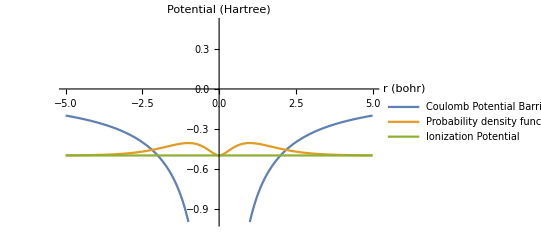

```mathematica
potWall[x_] :=-(cConst)(eCharge)Abs[1/(x )]- Efield*(0.2 x ); 
extF[a_] :=-0.2 Efield*(a ); 
wave[b_]:=(27.212)b^2 ((1/(2*Pi))*(1/a0)^(0 3/2)*Exp[-(Abs[b])/a0])^2 -ip; (*to change to SI take out 27.212eV factor and use SI contant names*)

Plot[{potWall[x]+Efield*(0.2 x ), wave[x],-ip } , {x,-5,5}, AxesLabel->{ "r (bohr)", "Potential (Hartree)"} , PlotLegends->{"Coulomb Potential Barrier","Probability density function of wave equation", "Ionization Potential"},  PlotRange -> {-1,.5}](*Change bounds appropriately*)
```

Figure 2: In the plot above, no electric field is applied to the system, so the well binds the electron to the atom and the atom does not become ionized.

### Tunneling Ionization

This section shows two plots using the same equations defined in the previous section: 1.) Tunneling ionization with an applied electric field, and 2.) the Wave function under the asymmetric coulomb potential barrier.

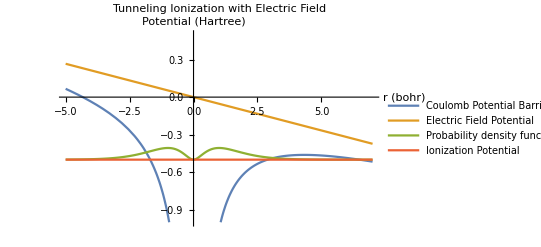

```mathematica
Plot[{potWall[x], extF[x], wave[x],-ip } , {x,-5,7}, AxesLabel->{ "r (bohr)", "Potential (Hartree)"} , PlotLegends->{"Coulomb Potential Barrier", "Electric Field Potential","Probability density function of Wave equation", "Ionization Potential"}, PlotLabel -> "Tunneling Ionization with Electric Field",PlotRange -> {-1,.5}](*Change bounds appropriately*)
```

Figure 3: The applied electric field suppresses the atomic potential asymmetrically, allowing for tunneling to occur through one side of the potential barrier. The end behavior of the coulomb potential barrier is asymptotic, in nature, along the Electric Field Potential line.

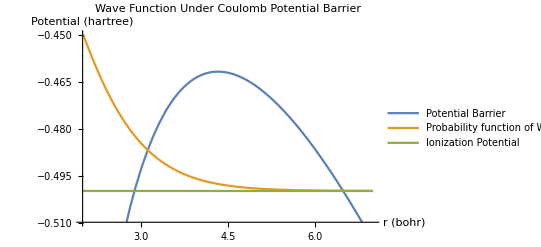

```mathematica
Plot[{potWall[x],  wave[x],-ip } , {x,2,7}, AxesLabel->{ "r (bohr)", "Potential (hartree)"} , PlotLegends->{"Potential Barrier","Probability function of Wave equation", "Ionization Potential"}, PlotRange -> {-.01-ip,.05-ip}, PlotLabel->"Wave Function Under Coulomb Potential Barrier" ]
(*See fig. 2 to change bounds appropriately*)
```

Figure 4: Under the barrier, the wave function continues. The remaining portion of the wave past the barrier signifies the atom’s probability to ionize through tunneling.

### ADK Analytical closed form expression for tunneling rate of hydrogen-like atoms under the barrier

This section shows the tunneling rate calculation for the applied electric field as defined above.

```mathematica
IR[elect_] := 6*ω0*(2*ip)((2/3)((2*ip)^(3/2))/elect)*Exp[-1 *Abs[((2/3)((2*ip)^(3/2))/elect)]];
```

```mathematica
IRcurrent = IR[Efield]
```

1.23005

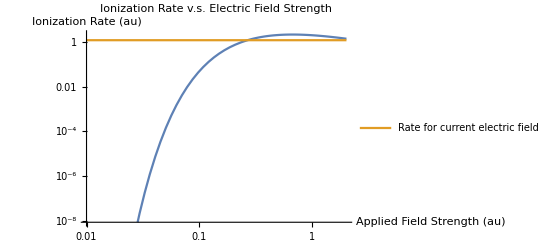

```mathematica
LogLogPlot[{IR[x],IRcurrent}, {x,.01,2}, AxesLabel ->{ "Applied Field Strength (au)", "Ionization Rate (au)"}, PlotLabel->"Ionization Rate v.s. Electric Field Strength" , PlotLegends->{None ,"Rate for current \n electric field in calc"}]
```

Ionization rate of a single electron system cannot be higher than the natural frequency of the revolution of an electron.